```mathematica
(* set up the Levy alpha-stable SDE *)
α=1.5;
(* drift *)
(* f[x_] := Sin[x] *)
(* f[{x_,y_}]:={y,-Sin[x]}; *)
f[{x_,y_}]:={x-x^3-x y^2,-(1+x^2)*y}
(* constant diffusion *)
g=1.0;
```

```mathematica
Integrate[(x-x^3-x y^2)Exp[-I k x/2],{x,-2π,2π}]
```

-(8 ⅈ (k π (-24+k^2 (-1+4 π^2+y^2)) Cos[k π]+(24-k^2 (-1+12 π^2+y^2)) Sin[k π]))/k^4

```mathematica
FullSimplify[%, Assumptions->{k∈Integers}]
```

-(8 ⅈ (-1)^k π (-24+k^2 (-1+4 π^2+y^2)))/k^3

```mathematica
Expand[%]
```

(192 ⅈ (-1)^k π)/k^3+(8 ⅈ (-1)^k π)/k-(32 ⅈ (-1)^k π^3)/k-(8 ⅈ (-1)^k π y^2)/k

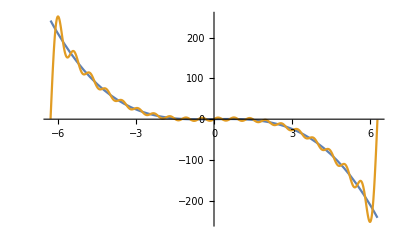

```mathematica
Plot[{x-x^3,Sum[If[k==0,0,((192 ⅈ (-1)^k π)/k^3+(8 ⅈ (-1)^k π)/k-(32 ⅈ (-1)^k π^3)/k)]Exp[I k x/2]/(4 π),{k,-20,20}]},{x,-2π,2π}]
```

```mathematica
(* phase plot for deterministic system *)
```

```mathematica
gettraj[i_]:=Block[
{mysol},mysol=NDSolve[{{x'[t],y'[t]}==f[{x[t],y[t]}],{x[0],y[0]}==ic[[i]]},{x[t],y[t]},{t,0,16π},PrecisionGoal->16];
ParametricPlot[{x[t],y[t]}/.mysol,{t,0,100},PlotRange->{{-1,1},{-1,1}}]
]
```

```mathematica
numtraj=15;
icmin=-1.0;
icmax=1.0;
ic=Table[{icmin+ (i-1) (icmax-icmin)/(numtraj-1),icmin+(j-1)(icmax-icmin)/(numtraj-1)},{i,1,numtraj},{j,1,numtraj}];
ic=Flatten[ic,1];
nic=Length[ic];
```

```mathematica
trajectories=Table[gettraj[i],{i,1,nic}];
```

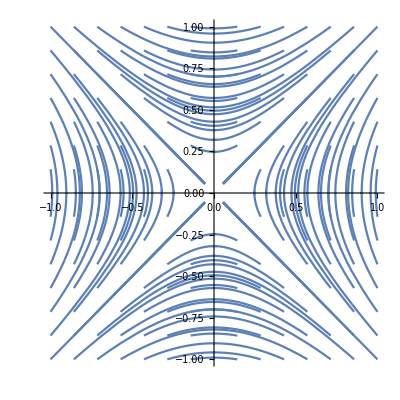

```mathematica
phaseplot=Show[trajectories]
```

```mathematica
(*dlmat=Transpose[{RandomVariate[StableDistribution[1,α,0.0,0.0,dt g],20],
RandomVariate[StableDistribution[1,α,0.0,0.0,dt g],20]}]
flres=FoldList[#1 + dt f[#1]+#2 &,{0.5,0},dlmat];
flres*)
```

```mathematica
(*ns=20;
mcsol=Table[{0,0},ns+1];
mcsol[[1]]={0.5,0};
For[i=1,i≤ns,i+=1,mcsol[[i+1]] =mcsol[[i]]+ (dt*f[mcsol[[i]]] +  dlmat[[i]]);
];
mcsol*)
```

```mathematica
cf=Compile[{{x,_Real,1}},f[x]]
```

CompiledFunction[…]

```mathematica
cf[{5.0,3.0}]
```

{-165.,-78.}

```mathematica
f[{5.0,3.0}]
```

{-165.,-78.}

```mathematica
icarr=Table[{-1 + 2/9 (i-1),-1 + 2/9 (j-1)},{i,1,10},{j,1,10}];
```

```mathematica
icarr2=ArrayReshape[icarr,{100,2}];
```

```mathematica
ntraj=100;
nsamp=1;
(* plots=Table[{},{i,ntraj}]; *)
dt = 0.0001;
ns = 100000;
tvec=Table[j*dt,{j,0,ns}];
For[traj=1,traj≤ntraj,traj+=1,
mcsol=Table[{0,0},ns+1];
ic=icarr2[[traj]];
keepgoing=True;
While[keepgoing==True,
dlmat=Transpose[{RandomVariate[StableDistribution[1,α,0.0,0.0,g (dt)^(1/α)],ns],
RandomVariate[StableDistribution[1,α,0.0,0.0,(dt)^(1/α) g],ns]}];
keepgoing=Check[FoldList[#1 + dt cf[#1]+#2 &,ic,dlmat],True]];
Print[Max[Abs[keepgoing]]];
mcsol=keepgoing;
(*For[i=1,i≤ns,i+=1,mcsol[[i+1]] =mcsol[[i]]+ (dt*f[mcsol[[i]]] +  dlmat[[i]]);
]; *)
fname=StringJoin["maierstein2d",ToString[traj],".dat"];
myfile=OpenWrite[fname,BinaryFormat->True];
BinaryWrite[myfile,mcsol,"Real64"];
Close[myfile];Print[fname]
(* plots[[traj]]=ListPlot[mcsol]; *)
]
```

2.804

maierstein2d1.dat

10.6079

maierstein2d2.dat

20.6455

maierstein2d3.dat

5.49752

maierstein2d4.dat

7.47486

maierstein2d5.dat

14.6192

maierstein2d6.dat

5.10938

maierstein2d7.dat

4.0508

maierstein2d8.dat

9.07513

maierstein2d9.dat

2.48627

maierstein2d10.dat

10.5369

maierstein2d11.dat

4.50467

maierstein2d12.dat

3.07828

maierstein2d13.dat

2.2778

maierstein2d14.dat

4.16907

maierstein2d15.dat

24.3385

maierstein2d16.dat

3.15521

maierstein2d17.dat

10.5406

maierstein2d18.dat

3.76937

maierstein2d19.dat

2.4345

maierstein2d20.dat

3.58174

maierstein2d21.dat

4.69998

maierstein2d22.dat

7.99846

maierstein2d23.dat

8.39911

maierstein2d24.dat

4.1818

maierstein2d25.dat

7.05122

maierstein2d26.dat

13.898

maierstein2d27.dat

4.69643

maierstein2d28.dat

11.9305

maierstein2d29.dat

4.49103

maierstein2d30.dat

5.42103

maierstein2d31.dat

1.80777

maierstein2d32.dat

7.77293

maierstein2d33.dat

2.63284

maierstein2d34.dat

4.24267

maierstein2d35.dat

4.18686

maierstein2d36.dat

4.74931

maierstein2d37.dat

33.2091

maierstein2d38.dat

6.34192

maierstein2d39.dat

5.30846

maierstein2d40.dat

4.82251

maierstein2d41.dat

3.23872

maierstein2d42.dat

15.7636

maierstein2d43.dat

2.51986

maierstein2d44.dat

4.09341

maierstein2d45.dat

13.345

maierstein2d46.dat

17.502

maierstein2d47.dat

6.26912

maierstein2d48.dat

4.47808

maierstein2d49.dat

3.88407

maierstein2d50.dat

3.82287

maierstein2d51.dat

2.69862

maierstein2d52.dat

104.483

maierstein2d53.dat

4.11165

maierstein2d54.dat

27.6421

maierstein2d55.dat

18.5606

maierstein2d56.dat

3.96086

maierstein2d57.dat

12.4186

maierstein2d58.dat

7.94607

maierstein2d59.dat

3.15172

maierstein2d60.dat

5.04352

maierstein2d61.dat

4.11389

maierstein2d62.dat

14.4806

maierstein2d63.dat

6.49153

maierstein2d64.dat

10.7977

maierstein2d65.dat

5.82302

maierstein2d66.dat

8.67647

maierstein2d67.dat

4.42809

maierstein2d68.dat

5.2301

maierstein2d69.dat

8.92474

maierstein2d70.dat

6.71502

maierstein2d71.dat

3.03757

maierstein2d72.dat

8.08873

maierstein2d73.dat

20.6954

maierstein2d74.dat

8.77272

maierstein2d75.dat

2.63792

maierstein2d76.dat

6.08231

maierstein2d77.dat

5.76818

maierstein2d78.dat

13.7057

maierstein2d79.dat

9.01439

maierstein2d80.dat

4.60886

maierstein2d81.dat

2.92742

maierstein2d82.dat

14.4134

maierstein2d83.dat

4.42455

maierstein2d84.dat

2.73007

maierstein2d85.dat

4.02663

maierstein2d86.dat

3.80404

maierstein2d87.dat

7.01917

maierstein2d88.dat

2.89078

maierstein2d89.dat

3.28244

maierstein2d90.dat

11.3433

maierstein2d91.dat

2.94453

maierstein2d92.dat

5.13099

maierstein2d93.dat

25.9647

maierstein2d94.dat

5.50656

maierstein2d95.dat

3.51682

maierstein2d96.dat

2.10137

maierstein2d97.dat

10.6082

maierstein2d98.dat

18.9294

maierstein2d99.dat

6.85871

maierstein2d100.dat